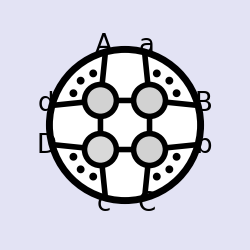
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<loop_amplitudes.m
n=9;
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c])};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>(Sort[i] Signature[i])/Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
myComplement[x_,y_]:=Select[x,!MemberQ[y,#]&];
```

```mathematica
randomPositiveZs[n_]:=(Zs=Nest[Function[{mat},Block[{hatted=Append[(Append[Total[mat⟦#1;;-1⟧],1]&)/@Range[2,Length[mat]],Append[PadRight[{},Length[mat⟦1⟧]],1]],newRow=RandomInteger[{1,10},{Length[mat]}]},newRow hatted]],RandomInteger[{1,10},{n+8,1}],3];Zs=Transpose[Inverse[Transpose[Zs⟦{1,2,3,4}⟧]].Transpose[Zs]]⟦5;;-1⟧;)
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
```

```mathematica
dabtoeta=dab[x__]:>Apply[ab,Partition[{x},4,1,5],{1}].η/@{x};
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};
repR1={R[cap[{a_,b_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1],R[cap[{b_,a_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1]};
repR2={R[cap[{a___},{c_,n,n+1}],d___,n+1,cap[{n,n+1},m__]]:>(ab[c,d,n+1]ab[a,n,n+1])/(ab[c,a,n+1]ab[d,n,n+1])R[c,cap[{a},{c,n,n+1}],d,n]R[a,c,n,n+1]};
qlogtodabm={Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n])};
numabfactor[exp_]:=ab@@@Subsets[Range[9],{4}][[Flatten[Position[exp/(ab@@@Subsets[Range[9],{4}])//neab,_Integer]]]];
dabsimp[exp_]:=Module[{f1,f2,f3},f1=exp/.dabcapexpand/.dabtoeta//neab//Simplify;
f2=dab@@(Cases[f1,η[_],Infinity]/.η->List//Flatten);
f3=Times@@(exp/f2/.dabcapexpand/.dabtoeta//neab//Simplify//numabfactor);
If[Abs[( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.i_η:>1//neab]<10,f2*f3 ( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.sortall,exp]
];

absim[exp_]:=Module[{f1},f1=Times@@(exp//numabfactor);
If[Abs[exp/f1//neab]<10,f1(exp/f1//neab),exp]
];
```

```mathematica
utoab={u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9]),a->(ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]),b->(ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,4,5])/(ab[9,cap1[{1,8},{2,3},{4,5}]] ab[4,5,6,7])};
tautre={τ->(-t^2-2 t(-1+u1) u+u^2 v1 (-2-2 u1+v1))/(t^2+2 t (-1+v) v1+(2+2 v-u) u v1^2)};
deltatau=(u^2+τ^2((1-u-v)^2-4u v)-2τ u v-2τ u+2τ u^2+2τ u/v1-2τ (u v)/v1-(2 u^2)/v1-2τ u^2/v1+u^2/v1^2+(u^2 u1^2)/v1^2-2τ (u u1)/v1-(2 u^2 u1)/v1^2-2(u^2 u1)/v1-2τ(u^2 u1)/v1+2τ (u v u1)/v1)/(τ+u/v1)^2;
(* 1-u-v-Δ= (4 u v1 (u ((-2+u) u1-v (-2+v1)) v1+t (u u1-v v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1))),1-u-v+Δ= -(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1))), integration range= [v1(1-v+Δ),u(1-u1+Δ1)] *)
deltat=-(t^2 (u (-1+u1)+v1-v v1)+u^2 v1^2 (u (-1+u1)-4 u1+4 v+v1-v v1)+2 t u v1 (u (1+u1)-(1+v) v1))/((t+u v1) (t (u-v1)+u v1 (-u-2 u1+2 v+v1)));
shiftm4=shift[{6,7},-(u(v1-(2 ab[2,3,8,9] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,8,9]))+t)/(u(v1-(2 ab[2,3,8,9] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,8,9]))+t) ab[2,3,6,9]/ab[2,3,7,9]];
shiftp4=shift[{6,7},-(-u v1(1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[cap[{2,3},{8,9,1}],4,5,6])+t)/(-u v1(1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[cap[{2,3},{8,9,1}],4,5,7])+t)ab[4,5,6,cap[{2,3},{8,9,1}]]/ab[4,5,7,cap[{2,3},{8,9,1}]]];
jacm4=-(4 u v1 (u ((-2+u) u1-v (-2+v1)) v1+t (u u1-v v1)))/(t^2 (u (-1+u1)+v1-v v1)+u^2 v1^2 (u (-1+u1)-4 u1+4 v+v1-v v1)+2 t u v1 (u (1+u1)-(1+v) v1));
jacp4=(2 (t-u v1) (t (u (-1+u1)+v1-v v1)+u v1 (u (1+u1)-(1+v) v1)))/((t^2+2 t (-1+v) v1+u (2-u+2 v) v1^2)^2);
```

```mathematica
scalarBoxIntegral[]
```

```mathematica
lastbox=(dlog[t-u v1 (1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,6}]])] Qlog[ab[8,9,1,cap[{2,3},{4,5,6}]]/ab[8,9,1,6]]-dlog[t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]+dlog[t-u v1] Qlog[ab[8,9,1,6]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,3,4,5,6]-(-dlog[t+(u v1 (u (1+u1)-(1+v) v1))/(u (-1+u1)+v1-v v1)] Qlog[ab[8,9,1,cap[{2,3},{4,5,6}]]/ab[8,9,1,3]]+dlog[t-u v1 (-1+(2 ab[2,3,6,7] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{2,3},{4,5,6}]]/ab[8,9,1,6]]-dlog[t-u v1 (-1+(2 ab[2,3,6,7] ab[3,4,5,9])/ab[3,cap1[{4,5},{6,7},{2,9}]])] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]+dlog[t-u v1 (-1+(2 ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]))] Qlog[ab[8,9,1,6]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,3,4,5,6]+(-dlog[t-u v1 (1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,7}]])] Qlog[ab[8,9,1,cap[{2,3},{4,5,7}]]/ab[8,9,1,7]]+dlog[t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]+dlog[t-u v1] Qlog[ab[8,9,1,cap[{6,7},{3,4,5}]]/ab[8,9,1,7]]) R[2,3,4,5,7]+(-dlog[t+(u v1 (u (1+u1)-(1+v) v1))/(u (-1+u1)+v1-v v1)] Qlog[ab[8,9,1,cap[{2,3},{4,5,7}]]/ab[8,9,1,3]]+dlog[t-u v1 (-1+(2 ab[2,3,6,7] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{2,3},{4,5,7}]]/ab[8,9,1,7]]-dlog[t-u v1 (1+(2 ab[2,3,4,5] ab[3,6,7,9])/ab[3,cap1[{2,9},{4,5},{6,7}]])] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]-dlog[t-u v1 (-1+(2 ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{6,7},{3,4,5}]]/ab[8,9,1,7]]) R[2,3,4,5,7]-(-dlog[t+u v1 (1+(2 ab[1,4,8,9] ab[2,3,6,7])/ab[8,9,1,cap[{2,3},{4,6,7}]])] Qlog[ab[8,9,1,cap[{2,3},{4,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,4}]]]+dlog[t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]-dlog[t-u v1] Qlog[ab[8,9,1,cap[{6,7},{2,3,4}]]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,3,4,6,7]-(-dlog[t+(u v1 (u (1+u1)-(1+v) v1))/(u (-1+u1)+v1-v v1)] Qlog[ab[8,9,1,cap[{2,3},{4,6,7}]]/ab[8,9,1,3]]+dlog[t-u v1 (1-(2 ab[2,3,4,5] ab[4,6,7,9])/(ab[2,3,4,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{2,3},{4,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,4}]]]-dlog[t-u v1 (-1+(2 ab[2,3,6,7] ab[3,4,5,9])/ab[3,cap1[{4,5},{6,7},{2,9}]])] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]+dlog[t-u v1 (-1+(2 ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{6,7},{2,3,4}]]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,3,4,6,7]+(-dlog[t+u v1 (1+(2 ab[1,5,8,9] ab[2,3,6,7])/ab[8,9,1,cap[{2,3},{5,6,7}]])] Qlog[ab[8,9,1,cap[{2,3},{5,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,5}]]]+dlog[t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]-dlog[t-u v1] Qlog[ab[8,9,1,cap[{6,7},{2,3,5}]]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,3,5,6,7]-(dlog[t+(u v1 (u (1+u1)-(1+v) v1))/(u (-1+u1)+v1-v v1)] Qlog[ab[8,9,1,cap[{2,3},{5,6,7}]]/ab[8,9,1,3]]-dlog[t-u v1 (1-(2 ab[2,3,4,5] ab[5,6,7,9])/(ab[2,3,5,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{2,3},{5,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,5}]]]+dlog[t+u v1-(2 u v1 ab[2,3,6,7] ab[3,4,5,9])/ab[3,cap1[{4,5},{6,7},{2,9}]]] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]-dlog[t+u v1-(2 u v1 ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7])] Qlog[ab[8,9,1,cap[{6,7},{2,3,5}]]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,3,5,6,7]-(-dlog[t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{2,4,5}]])/(ab[1,2,8,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,2]/ab[8,9,1,cap[{6,7},{2,4,5}]]]+dlog[t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7]))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]-dlog[t-u v1] Qlog[ab[8,9,1,cap[{6,7},{2,4,5}]]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,4,5,6,7]-(-dlog[t+(u v1 (u (1+u1)-(1+v) v1))/(u (-1+u1)+v1-v v1)] Qlog[ab[8,9,1,2]/ab[8,9,1,3]]+dlog[t-u v1 (1-(2 ab[2,3,4,5] ab[2,6,7,9])/ab[2,cap1[{4,5},{6,7},{3,9}]])] Qlog[ab[8,9,1,2]/ab[8,9,1,cap[{6,7},{2,4,5}]]]-dlog[t-u v1 (-1+(2 ab[2,3,6,7] ab[3,4,5,9])/ab[3,cap1[{4,5},{6,7},{2,9}]])] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]]+dlog[t-u v1 (-1+(2 ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]))] Qlog[ab[8,9,1,cap[{6,7},{2,4,5}]]/ab[8,9,1,cap[{6,7},{3,4,5}]]]) R[2,4,5,6,7];lastbox=lastbox/.{t+(u v1 (u (1+u1)-(1+v) v1))/(u (-1+u1)+v1-v v1):>t- u v1 (a+b)/(a-b),(ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]):>a};
```

```mathematica
lastboxsim=dlog[(t-u v1 (1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,6}]]))/(t+u v1 (1-(2 ab[2,3,6,7] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,6,7])))] Qlog[ab[8,9,1,cap[{2,3},{4,5,6}]]/ab[8,9,1,6]] R[2,3,4,5,6]+dlog[(t+u v1 (1-(2 ab[2,3,6,7] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,6,7])))/(t-u v1 (1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,7}]]))] Qlog[ab[8,9,1,cap[{2,3},{4,5,7}]]/ab[8,9,1,7]] R[2,3,4,5,7]+dlog[(t+u v1+(2 u v1 ab[1,4,8,9] ab[2,3,6,7])/ab[8,9,1,cap[{2,3},{4,6,7}]])/(t+u v1 (-1+(2 ab[2,3,4,5] ab[4,6,7,9])/(ab[2,3,4,9] ab[4,5,6,7])))] Qlog[ab[8,9,1,cap[{2,3},{4,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,4}]]] R[2,3,4,6,7]+dlog[(t+u v1 (-1+(2 ab[2,3,4,5] ab[5,6,7,9])/(ab[2,3,5,9] ab[4,5,6,7])))/(t+u v1+(2 u v1 ab[1,5,8,9] ab[2,3,6,7])/ab[8,9,1,cap[{2,3},{5,6,7}]])] Qlog[ab[8,9,1,cap[{2,3},{5,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,5}]]] R[2,3,5,6,7]+dlog[(t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{2,4,5}]])/(ab[1,2,8,9] ab[4,5,6,7])))/(t-u v1+(2 u v1 ab[2,3,4,5] ab[2,6,7,9])/ab[2,cap1[{4,5},{6,7},{3,9}]])] Qlog[ab[8,9,1,2]/ab[8,9,1,cap[{6,7},{2,4,5}]]] R[2,4,5,6,7]+dlog[(t+u v1-(2 u v1 ab[2,3,6,7] ab[3,4,5,9])/ab[3,cap1[{4,5},{6,7},{2,9}]])/(t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7])))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]] R[3,4,5,6,7]+dlog[(t-u v1)/(t+(1-2 a) u v1)]Qlog[ab[8,9,1,6]/ab[8,9,1,7]] R[2,3,4,5,cap[{6,7},{8,9,1}]]+dlog[t-((a+b) u v1)/(a-b)]Qlog[ab[8,9,1,2]/ab[8,9,1,3]] R[6,7,4,5,cap[{2,3},{8,9,1}]]/.{u->(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),v->(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),u1->(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),v1->(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9]),a->(ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,6,7])/(ab[9,cap1[{1,8},{2,3},{6,7}]] ab[4,5,6,7]),b->(ab[9,cap1[{1,8},{4,5},{6,7}]] ab[2,3,4,5])/(ab[9,cap1[{1,8},{2,3},{4,5}]] ab[4,5,6,7])};
```

```mathematica
(* Check lastbox and lastboxsim equal *)
```

```mathematica
randomPositiveZs[20];
```

```mathematica
Table[(fuse[(lastbox-lastboxsim)/.dlog[x_]:>D[Log[x],t]/.utoab/.sortab/.qlogtodab//.dabcapexpand//todmatrixn//todoubleab]//neabp)/.dabne[{i,j}]/.DmatrixEval3[{7,7,7},3]//Simplify,{i,1,7},{j,i+1,8}]
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0},{0,0,0,0},{0,0,0},{0,0},{0}}

```mathematica
boxfun4=Li[(t-u v1)/(t+u v1)]-Li[(b/a (t-u v1(-1+2a))/(t-u v1(1+2b)))]+1/2 log[(b/a (t-u v1(-1+2a))/(t-u v1(1+2b)))(t-u v1)/(t+u v1)] log[(1-(t-u v1)/(t+u v1))/(1-(b/a (t-u v1(-1+2a))/(t-u v1(1+2b))))];
```

```mathematica
(* Check two box functions equal *)
```

```mathematica
randomPositiveZs[20];
```

4.44089×10^-16

```mathematica
(* Check boxcoefficient after variable substitution *)
```

```mathematica
origincoe1=fuse[Numerator[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[{6,5}]/.DmatrixEval3[{7,7,7},3];subcoef1=Simplify[Limit[(1/2+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))/(2 √(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2))//fullabB//neabp),e->0]/.tautre/.utoab//neabp,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab]<t<neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]]*Simplify[Limit[Simplify[origincoe1,τ>0],e->0]/.tautre/.utoab//neabp,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab]<t<neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]];
origincoe2=fuse[Numerator[Total[rForm[onShellGraph[2][{{3,4},{5,6},{7,8,9},{10,1,2}},{0,0,0,0}]]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[{6,5}]/.DmatrixEval3[{7,7,7},3];
subcoef2=Simplify[Limit[-(1/2-(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))/(2 √(-(4 ab[2,3,4,5] ab[4,5,6,7] ab[6,7,9,10] ab[9,10,2,3])/(ab[2,3,6,7]^2 ab[4,5,9,10]^2)+(1-(ab[2,3,4,5] ab[6,7,9,10])/(ab[2,3,6,7] ab[4,5,9,10])-(ab[4,5,6,7] ab[9,10,2,3])/(ab[2,3,6,7] ab[4,5,9,10]))^2))//fullabB//neabp),e->0]/.tautre/.utoab//neabp,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab]<t<neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]]*Simplify[Limit[Simplify[origincoe2,τ>0],e->0]/.tautre/.utoab//neabp,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab]<t<neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]];
subcoef=subcoef1+subcoef2;
((fuse[lastbox/.utoab/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[{6,5}]/.DmatrixEval3[{7,7,7},3]//Simplify)-(ab[2,3,8,9]/ab[1,2,3,9] D[τ/.tautre,t]/.utoab//neabp)subcoef//Simplify
```

0

```mathematica
tautre
```

{τ→(-t^2-2 t u (-1+u1)+u^2 v1 (-2-2 u1+v1))/(t^2+2 t (-1+v) v1+u (2-u+2 v) v1^2)}

```mathematica
{u,u1,v,v1}/.utoab
```

{(ab[1,2,3,9] ab[4,5,6,7])/(ab[1,4,5,9] ab[2,3,6,7]),(ab[2,3,4,5] ab[6,7,8,9])/(ab[2,3,6,7] ab[4,5,8,9]),(ab[1,6,7,9] ab[2,3,4,5])/(ab[1,4,5,9] ab[2,3,6,7]),(ab[4,5,6,7] ab[8,9,2,3])/(ab[2,3,6,7] ab[4,5,8,9])}

```mathematica
Simplify[Solve[(-t^2-2 t u (-1+u1)+u^2 v1 (-2-2 u1+v1))/(t^2+2 t (-1+v) v1+u (2-u+2 v) v1^2)==τ,t],τ>0]
```

```mathematica
lastboxsim
```

dlog[(t-u v1 (1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,6}]]))/(t+u v1 (1-(2 ab[2,3,6,7] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,6,7])))] Qlog[ab[8,9,1,cap[{2,3},{4,5,6}]]/ab[8,9,1,6]] R[2,3,4,5,6]+dlog[(t+u v1 (1-(2 ab[2,3,6,7] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,6,7])))/(t-u v1 (1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,7}]]))] Qlog[ab[8,9,1,cap[{2,3},{4,5,7}]]/ab[8,9,1,7]] R[2,3,4,5,7]+dlog[(t-u v1)/(t+(1-2 a) u v1)] Qlog[ab[8,9,1,6]/ab[8,9,1,7]] R[2,3,4,5,cap[{6,7},{8,9,1}]]+dlog[(t+u v1+(2 u v1 ab[1,4,8,9] ab[2,3,6,7])/ab[8,9,1,cap[{2,3},{4,6,7}]])/(t+u v1 (-1+(2 ab[2,3,4,5] ab[4,6,7,9])/(ab[2,3,4,9] ab[4,5,6,7])))] Qlog[ab[8,9,1,cap[{2,3},{4,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,4}]]] R[2,3,4,6,7]+dlog[(t+u v1 (-1+(2 ab[2,3,4,5] ab[5,6,7,9])/(ab[2,3,5,9] ab[4,5,6,7])))/(t+u v1+(2 u v1 ab[1,5,8,9] ab[2,3,6,7])/ab[8,9,1,cap[{2,3},{5,6,7}]])] Qlog[ab[8,9,1,cap[{2,3},{5,6,7}]]/ab[8,9,1,cap[{6,7},{2,3,5}]]] R[2,3,5,6,7]+dlog[(t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{2,4,5}]])/(ab[1,2,8,9] ab[4,5,6,7])))/(t-u v1+(2 u v1 ab[2,3,4,5] ab[2,6,7,9])/ab[2,cap1[{4,5},{6,7},{3,9}]])] Qlog[ab[8,9,1,2]/ab[8,9,1,cap[{6,7},{2,4,5}]]] R[2,4,5,6,7]+dlog[(t+u v1-(2 u v1 ab[2,3,6,7] ab[3,4,5,9])/ab[3,cap1[{4,5},{6,7},{2,9}]])/(t-u v1 (1+(2 ab[8,9,1,cap[{6,7},{3,4,5}]])/(ab[1,3,8,9] ab[4,5,6,7])))] Qlog[ab[8,9,1,3]/ab[8,9,1,cap[{6,7},{3,4,5}]]] R[3,4,5,6,7]+dlog[t-((a+b) u v1)/(a-b)] Qlog[ab[8,9,1,2]/ab[8,9,1,3]] R[6,7,4,5,cap[{2,3},{8,9,1}]]

```mathematica
NIntegrate[dlog[t-((a+b) u v1)/(a-b)]boxfun4/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}/.utoab//neabp,{t,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab],neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]},WorkingPrecision->30]
```

15.6051539690658802008926446819

```mathematica
dlog[t-((a+b) u v1)/(a-b)]boxfun4/.u:>uv/v1/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}
```

```mathematica
(* symbol of dlog[t-((a+b) u v1)/(a-b)]boxfun4 *)
sym1=1/2 (Tensor[(-1+z) (-1+z̄),z,((-1+z) z̄)/(z (-1+a z̄))]+Tensor[(-1+z) (-1+z̄),a z,1-a+b]+Tensor[(-1+z) (-1+z̄),z̄,(b z (-1+a z̄))/(a (-1+z) z̄)]+Tensor[z z̄,1-z,(b z (-1+a z̄))/(a (-1+z) z̄)]+Tensor[z z̄,b/(a-a z),1-a+b]+Tensor[z z̄,1-z̄,((-1+z) z̄)/(z (-1+a z̄))]+Tensor[z z̄,z z̄,a/b]+Tensor[(-1+ζ) (-1+ζ̄),ζ,(a (b (-1+ζ)+ζ) (-1+ζ̄))/(b (-1+ζ))]+Tensor[(-1+ζ) (-1+ζ̄),(-1+ζ) (-1+ζ̄),b/a]+Tensor[(-1+ζ) (-1+ζ̄),ζ̄,(1-ζ)/((b (-1+ζ)+ζ) (-1+ζ̄))]+Tensor[(-1+ζ) (-1+ζ̄),(a ζ̄)/b,1-a+b]+Tensor[ζ ζ̄,1-ζ,(1-ζ)/((b (-1+ζ)+ζ) (-1+ζ̄))]+Tensor[ζ ζ̄,1-ζ̄,(a (b (-1+ζ)+ζ) (-1+ζ̄))/(b (-1+ζ))]+Tensor[ζ ζ̄,1/(a-a ζ̄),1-a+b]);
```

```mathematica
Solve[{x+y==a,x-y==b},{x,y}]
```

{{x→(a+b)/2,y→(a-b)/2}}

```mathematica
NIntegrate[dlog[(t-u v1)/(t+(1-2 a) u v1)]boxfun4/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}/.utoab//neabp,{t,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab],neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]},WorkingPrecision->30]
```

-9.10693947213991663380425112418

```mathematica
dlog[(t-u v1)/(t+(1-2 a) u v1)]boxfun4/.u:>uv/v1/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}
```

((t+(1-2 a) uv) (-(t-uv)/(t+(1-2 a) uv)^2+1/(t+(1-2 a) uv)) (1/2 Log[(b (t-uv) (t-(-1+2 a) uv))/(a (t+uv) (t-(1+2 b) uv))] Log[(1-(t-uv)/(t+uv))/(1-(b (t-(-1+2 a) uv))/(a (t-(1+2 b) uv)))]+PolyLog[2,(t-uv)/(t+uv)]-PolyLog[2,(b (t-(-1+2 a) uv))/(a (t-(1+2 b) uv))]))/(t-uv)

```mathematica
(* symbol of dlog[(t-u v1)/(t+(1-2 a) u v1)]boxfun4 *)
```

```mathematica
sym2=1/2 (Tensor[1-z,z,a+(-1+a)/(-1+z̄)]+Tensor[1-z,a z,b/(1-a+b)]+Tensor[z,1-z,(-1+z̄)/(-1+a z̄)]+Tensor[z,a-a z,(1-a+b)/b]+Tensor[1-z̄,z,(b-a b z̄)/((-1+a-b) (-1+z̄))]+Tensor[(-1+z) (-1+z̄),((-1+z) (-1+z̄))/z,a]+Tensor[(-1+z) (-1+z̄),z̄,(-1+z̄)/(-1+a z̄)]+Tensor[z̄,1-z,((1-a+b) (-1+z̄))/(b (-1+a z̄))]+Tensor[z z̄,b,b/(1-a+b)]+Tensor[z z̄,1-z̄,1+(-1+a)/(a (-1+z̄))]+Tensor[(-1+ζ) (-1+ζ̄),b,(1-a+b)/b]+Tensor[(-1+ζ) (-1+ζ̄),ζ,(b ζ)/((b (-1+ζ)+ζ) ζ̄)]+Tensor[(-1+ζ) (-1+ζ̄),ζ̄,(a (b (-1+ζ)+ζ) ζ̄)/((-1+a-b) ζ)]+Tensor[(-1+ζ) (-1+z̄) (-1+ζ̄),a,b/(1-a+b)]+Tensor[ζ ζ̄,1-ζ,(a (b (-1+ζ)+ζ) ζ̄)/(b ζ)]+Tensor[ζ ζ̄,1-ζ̄,((-1+a-b) ζ)/((b (-1+ζ)+ζ) ζ̄)]+Tensor[ζ ζ̄,1/(ζ ζ̄),a]+Tensor[ζ z̄ ζ̄,a,(1-a+b)/b]);
```

```mathematica
NIntegrate[dlog[(t-u v1 (1+(2 ab[1,6,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,6}]]))/(t+u v1 (1-(2 ab[2,3,6,7] ab[4,5,6,9])/(ab[2,3,6,9] ab[4,5,6,7])))]boxfun4/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}/.utoab//neabp,{t,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab],neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]},WorkingPrecision->30]
```

-1.63137445303731669198732635984

```mathematica
dlog[(t-u v1 (1+2x))/(t+u v1 (1-2 y))] boxfun4/.u:>uv/v1/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}
```

((-(t-uv (1+2 x))/(t+uv (1-2 y))^2+1/(t+uv (1-2 y))) (t+uv (1-2 y)) (1/2 Log[(b (t-uv) (t-(-1+2 a) uv))/(a (t+uv) (t-(1+2 b) uv))] Log[(1-(t-uv)/(t+uv))/(1-(b (t-(-1+2 a) uv))/(a (t-(1+2 b) uv)))]+PolyLog[2,(t-uv)/(t+uv)]-PolyLog[2,(b (t-(-1+2 a) uv))/(a (t-(1+2 b) uv))]))/(t-uv (1+2 x))

```mathematica
NIntegrate[dlog[(t+u v1 (1-(2 ab[2,3,6,7] ab[4,5,7,9])/(ab[2,3,7,9] ab[4,5,6,7])))/(t-u v1 (1+(2 ab[1,7,8,9] ab[2,3,4,5])/ab[8,9,1,cap[{2,3},{4,5,7}]]))]boxfun4/.dlog[x_]:>D[Log[x],t]/.{Li[x_]:>PolyLog[2,x],log:>Log}/.utoab//neabp,{t,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab],neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]},WorkingPrecision->30]
```

4.79793187005020861558400742776

```mathematica
Zs
```

{{-45/8,363/16,-1573/48,959/60},{-675/56,2691/56,-3691/56,279/10},{-1065/28,16951/112,-23147/112,347/4},{-3391/224,33541/560,-27149/336,1993/60},{-6831/28,67117/70,-89491/70,2582/5},{-13631/28,133187/70,-528083/210,15046/15},{-489,38139/20,-50247/20,4989/5},{-18135/14,140927/28,-554329/84,7813/3},{-351675/224,3410181/560,-4461171/560,62691/20},{-48345/28,468297/70,-367069/42,10298/3},{-65241/112,126165/56,-2467057/840,34513/30},{-35037/16,338319/40,-440353/40,43039/10},{-842193/224,8126361/560,-2113695/112,147411/20},{-486165/224,1875987/224,-2439139/224,34011/8},{-116933/112,281719/70,-731741/140,10189/5},{-450759/112,542352/35,-2813757/140,39117/5},{-226485/32,435735/16,-2823813/80,274563/20},{-189337/56,3641713/280,-4718729/280,65521/10},{-194247/56,186789/14,-363007/21,100796/15},{-1022155/224,1965429/112,-7637617/336,106009/12},{-255497/112,4908609/560,-19057547/1680,264227/60},{-301673/112,5792673/560,-7492409/560,103809/20},{-240927/28,18501111/560,-23924667/560,66279/4},{-182269/28,6995361/280,-9042053/280,125181/10}}